JSON Import

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

```mathematica
ImportJSONData[files_]:=Module[{},
Switch[Head[files],
String,
Import[files,"RawJSON"],
List,
Import[#,"RawJSON"]&/@files
]
];
OpenJSONData[]:=Module[{files},
files=OpenJSONDialog[];
ImportJSONData[files]
];
```

Visualize and process input JSON

### Plots simulation data structure. Single or list of simulations data

```mathematica
plotSimData[data_, color_:RGBColor[0.368417, 0.506779, 0.709798],legend_:"" ]:=
ListPlot[
Flatten[data["Trees"]["Branches"][[All,"coords"]],{1}],
Joined->True,
PlotRange->{{0,(*data["Model", "width"]*)2},{0,(*data["Model", "height"]*)5.5}}, 
AspectRatio->1, 
PlotStyle->color,
(*PlotLegends->{legend},*)
AxesLabel->{"X","Y"}];
```

```mathematica
plotJSON[filePath_]:=
plotSimData[Import[filePath, "RawJSON"]];
```

Cut and compare rivers

```mathematica
cutRivers[data_, fileName_]:=Module[{initialDistance,toDrop,dataExport},
initialDistance = EuclideanDistance[#1,#2]&@@data["Trees","Branches"][[All,2,1]];
toDrop=Count[MapThread[EuclideanDistance,data["Trees","Branches"][[All,2]]],u_/;u>3initialDistance];
dataExport=data;
dataExport[[6,1,All,2]]=Drop[#,-toDrop]&/@data["Trees","Branches"][[All,2]];
Export[NotebookDirectory[]<>fileName,dataExport];
dataExport]
```

```mathematica
compare1[datas_, range_]:=Module[{savedOpt=Options[ListPlot],image,lbl=Style["η = "<>ToString[Row[(range-1)/10.,", "]],Black, 16]},
SetOptions[ListPlot,
PlotRange->{{0,2},{0,10}},AspectRatio->2,ImageSize->500,
Joined->True,Frame->{{True,True},{True,False}},FrameLabel->{{None,None},{lbl,None}},FrameTicksStyle->Directive[Black,16],
PlotStyle->Flatten[Table[Table[Directive[ColorData[97,"ColorList"][[i]],Thickness[0.01]],datas[[range[[i]],6,1,All,2]]//Length],{i,1,range//Length}]]];
image=ListPlot[Flatten[Table[Flatten[datas[[i,6,1,All,2]],{1}],{i,range}],1]];
SetOptions[ListPlot,savedOpt];
image]
```

```mathematica
compareRow[datas_, range_]:=Module[{image},
image=GraphicsRow[
Table[compare1[datas,{i}],{i,range}],
ImageSize->1200];
image]
```

```mathematica
compare15[datas_]:=Module[{image},
image=GraphicsRow[
Table[compare1[datas,{3*i+1,3*i+2,3*i+3}],{i,0,4}],
ImageSize->1200];
image]
```

```mathematica
compare20[datas_]:=Module[{image},
image=GraphicsGrid[{
Table[compare1[datas,{i}],{i,1,10}],
Table[compare1[datas,{i}],{i,11,20}]
},
ImageSize->800,Spacings->25];
image]
```

## Cutting rivers

```mathematica
datas=OpenJSONData[];
```

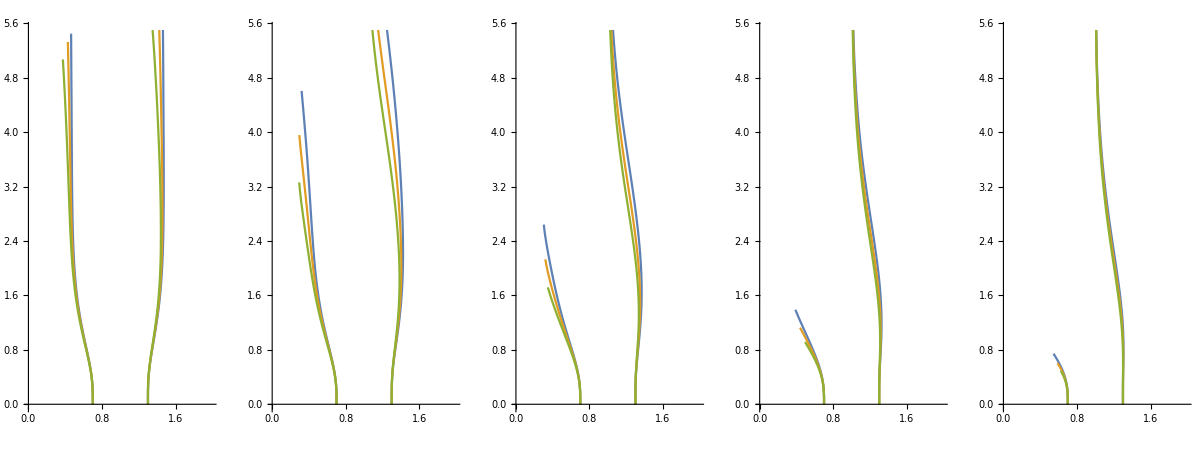

```mathematica
compare15[datas]
```

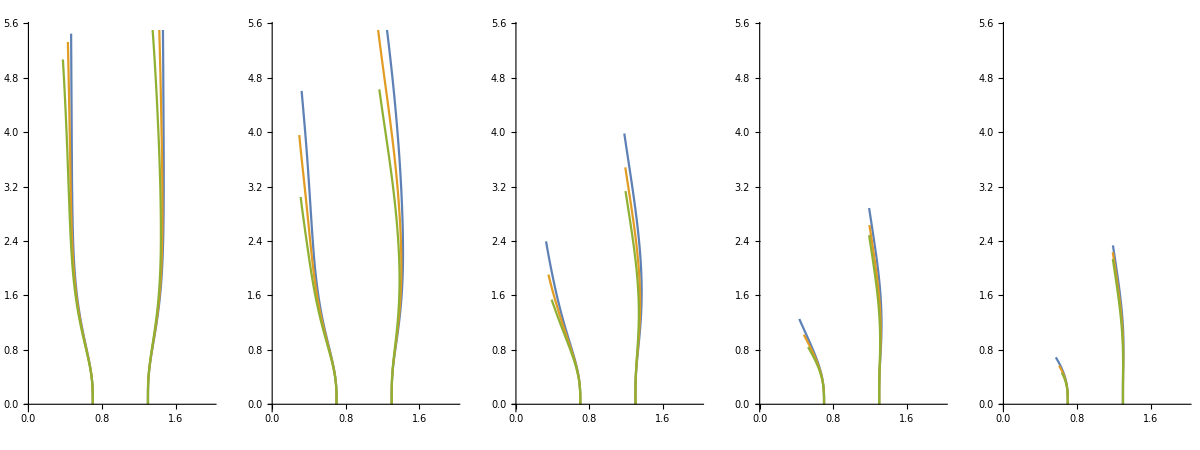

```mathematica
datasExport=MapThread[cutRivers,{datas,Table["initialLength1/cut_rivers/lap"<>ToString[index]<>".json",{index,Range@Length@datas}]}];compare15[datasExport]
```

Sandbox

```mathematica
datas=OpenJSONData[];
```

Part::partw: Part 10 of {«1»} does not exist.

Part::partw: Part 11 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

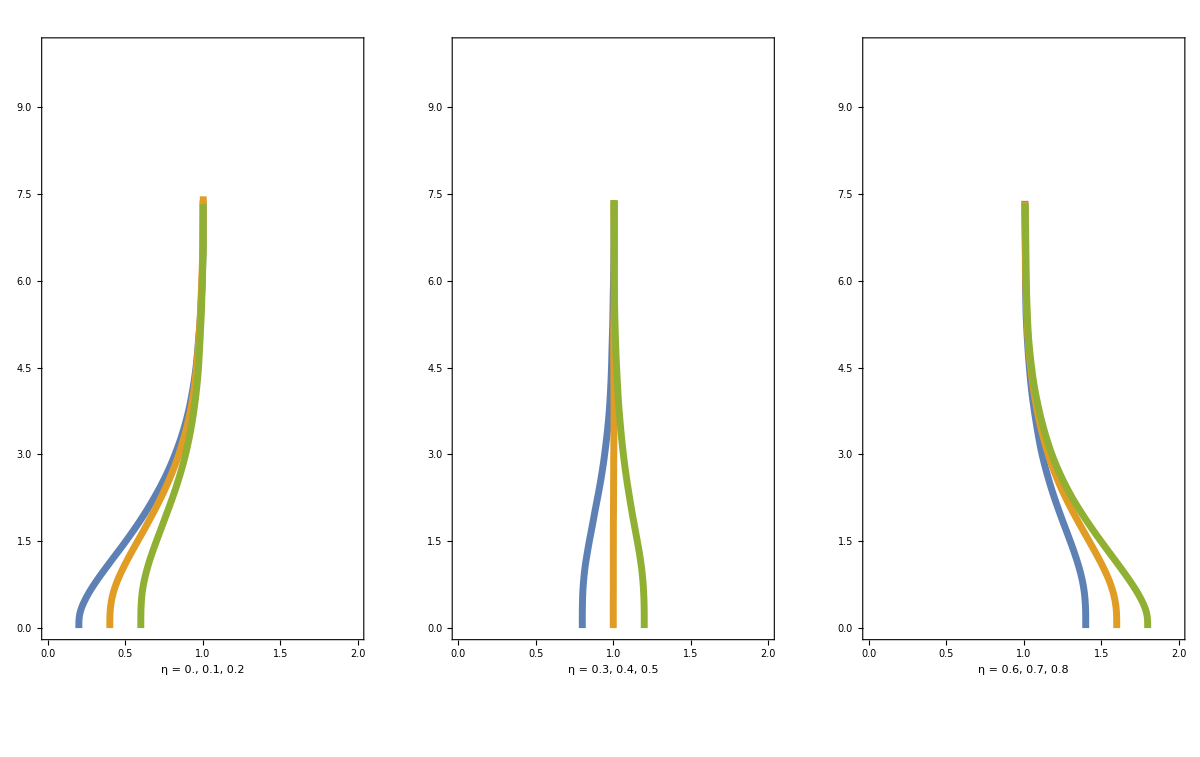

```mathematica
compare15[datas]
```

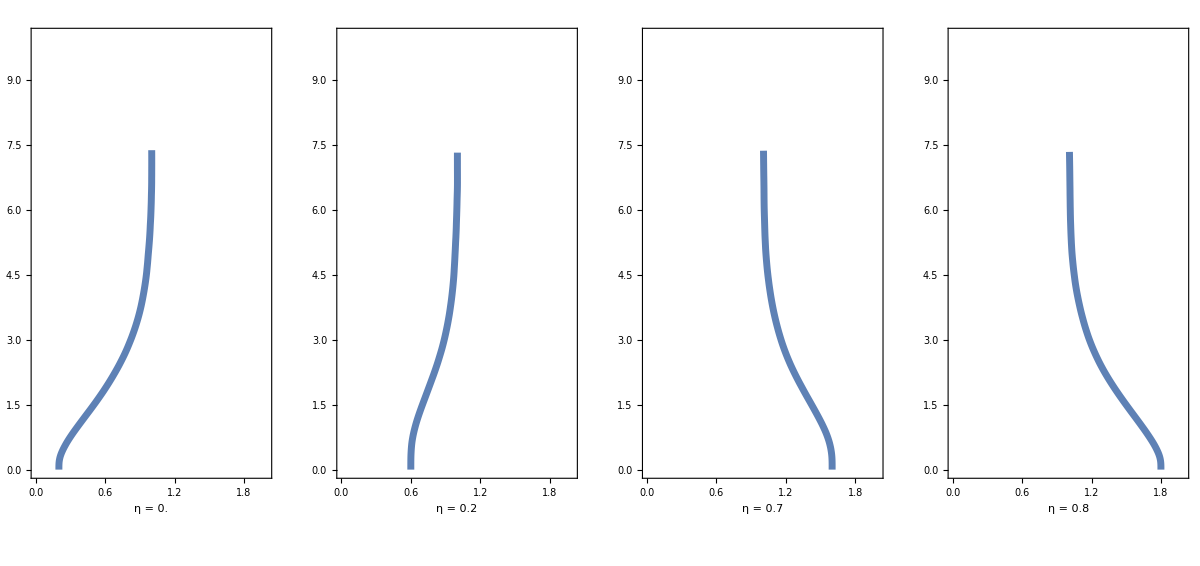

```mathematica
compareRow[datas,{1,3,8,9}]
```